# CKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\QKT\Fundamental symmetry lines and reflections

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[F,Fun,Funinv];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Funinv[α_,k_,s_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},-1].s
];
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];

Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];

Clear[mapeoinv];
mapeoinv[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funinv[α,k,#]&,s,n];
Map[change[#]&,list]
];

mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
Clear[T1,T2];
T1[theta_]:={{-Cos[theta],-Sin[theta]},{-Sin[theta],Cos[theta]}};
T2[theta_]:={{Cos[theta],Sin[theta]},{Sin[theta],-Cos[theta]}};
```

## Powers of Poincaré

```mathematica
Clear[Funp];
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}},p].s
];
Clear[mapeop];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Funp[α,k,#,p]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[α];
α=0.84;
τ=1;
```

```mathematica
radius=1.99999;
delta=0.02;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];*)
circlePoints=Select[gridPoints,Norm[#]<radius&];
(*randomregion=Join[boundaryPoints,circlePoints];
randomregionb=-randomregion;*)
region=circlePoints;
region//Length
```

31401

```mathematica
ListPlot[region,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=100;
p=1000;
```

```mathematica
k=15.;
```

```mathematica
puntosa=ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,region}];
newpoincarea=Flatten[puntosa,1];
powerone=Graphics[{PointSize[0.0020],Brown,Opacity[0.08],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
```

```mathematica
Export["test_k_"<>ToString[k]<>"_.png",powerone]
```

test_k_15._.png

## New clues

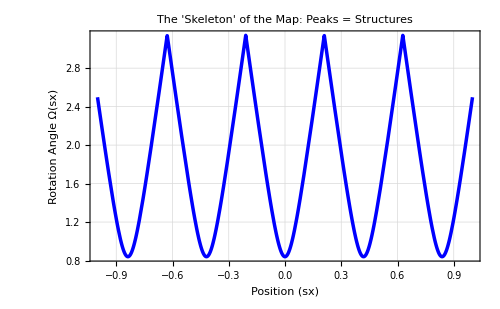

```mathematica
Clear[PlotOmega];
(*Define the Trace Function derived analytically*)
TraceM[α_,k_,sx_]:=Cos[α]+(1+Cos[α])*Cos[k*sx];

(*Define the Omega Function*)
OmegaFunc[α_,k_,sx_]:=ArcCos[(TraceM[α,k,sx]-1)/2];

(*Plot for specific parameters*)
Plot[OmegaFunc[0.84,15,sx],{sx,-1,1},Frame->True,FrameLabel->{"Position (sx)","Rotation Angle Ω(sx)"},PlotStyle->{Thickness[0.005],Blue},GridLines->Automatic,PlotLabel->"The 'Skeleton' of the Map: Peaks = Structures",ImageSize->500]
```

```mathematica
Manipulate[Module[{trace,omega,stationaryPoints},(*1. Define Functions*)trace[x_]:=Cos[α]+(1+Cos[α])*Cos[k*x];
omega[x_]:=ArcCos[(trace[x]-1)/2];
(*2. Find peaks/valleys analytically (where Sin[k sx]=0)*)(*The derivative is zero when sin(k*sx) is zero*)stationaryPoints=Select[Table[n*Pi/k,{n,-Ceiling[k/Pi],Ceiling[k/Pi]}],-1<=#<=1&];
(*3. Plot*)Show[Plot[omega[sx],{sx,-1,1},PlotRange->{0,Pi},Frame->True,FrameLabel->{"Position (sx)","Rotation Angle Ω"},PlotStyle->{Thick,Blue},GridLines->{stationaryPoints,None} (*Vertical lines at structures*)],(*Mark the structure centers*)Graphics[{PointSize[Large],Red,Point[{#,omega[#]}]&/@stationaryPoints}]]],{{k,5.0,"Nonlinearity (k)"},0.1,20},{{α,1.0,"Rotation (alpha)"},0,Pi}]
```

```mathematica
(*1. The Map Function (Same as your model)*)(*Returns the 3D point after the map*)MapPoint[s_,α_,k_,p_]:=Module[{sx,mat},sx=s[[1]];
mat={{Cos[α],-Sin[α] Cos[k sx],Sin[α] Sin[k sx]},{Sin[α],Cos[α] Cos[k sx],-Cos[α] Sin[k sx]},{0,Sin[k sx],Cos[k sx]}};
MatrixPower[mat,p].s];

(*2. Projection:3D Sphere->2D (Q,P)*)
(*Inverts your s=Q Sqrt[...] formula*)
ProjectToQP[s_]:={s[[1]]/Sqrt[(1+s[[3]])/2+10^-10],(*Q*)s[[2]]/Sqrt[(1+s[[3]])/2+10^-10]  (*P*)};

(*3. The Structure Generator*)
ShowRibbons[α_,k_,p_]:=Module[{criticalSx,lines,mappedLines},(*A.Find the Zero-Shear values:sx where Sin[k sx]==0*)criticalSx=Select[Table[n*Pi/k,{n,-Ceiling[k/Pi],Ceiling[k/Pi]}],-0.99<=#<=0.99&];
(*B.Create vertical lines of points at these sx values*)lines=Table[Table[{sx,Sqrt[1-sx^2] Sin[theta],Sqrt[1-sx^2] Cos[theta]},{theta,0,2 Pi,0.01}],{sx,criticalSx}];
(*C.Apply the Map M^p to every point in these lines*)mappedLines=Map[MapPoint[#,α,k,p]&,lines,{2}];
(*D.Project to Q,P for plotting*)mappedLines=Map[ProjectToQP,mappedLines,{2}];
(*E.Plot*)ListPlot[mappedLines,PlotStyle->{Red,Opacity[0.6],Thickness[0.005]},Joined->True,PlotRange->{{-2,2},{-2,2}},Frame->True,FrameLabel->{"Q","P"},AspectRatio->1,PlotLabel->Row[{"Skeleton: Forward Images of Zero-Shear (k=",k,")"}]]];

(*Interactive Explorer*)
Manipulate[ShowRibbons[α,k,p],{{k,15.0},1,20,Appearance->"Labeled"},(*Set to 15 to match your image*){{α,0.84},0,Pi},{{p,100},1,1000,1}]
```

```mathematica
(*1. Definitions and Setup*)
Clear[Funp,change,mapeop,Ribbons];

(*The Map Function M^p*)
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]],mat},mat={{Cos[α],-Sin[α] Cos[k*sx],Sin[α] Sin[k*sx]},{Sin[α],Cos[α] Cos[k*sx],-Cos[α] Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}};
MatrixPower[mat,p].s];
(*Projection:Sphere (s)->Plane (Q,P)*)
(*Derived as inverse of your s definition:Q=sx*Sqrt[2/(1-sz)]*)
change[s_]:=If[s[[3]]>=0.99999,{0.,0.},{s[[1]],s[[2]]}*Sqrt[2./(1.-s[[3]])]];
(*The Iterator:Generates trajectory for one point*)
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,R2=Norm[Qini]^2,s},s={Qini[[1]]*Sqrt[1-R2/4],Qini[[2]]*Sqrt[1-R2/4],R2/2-1};
list=NestList[Funp[α,k,#,p]&,s,n];
change/@list];
(*The Skeleton Generator:Forward Images of Zero-Shear Lines*)
Ribbons[α_,k_,p_]:=Module[{sxValues,lines,mappedLines},(*1. Find sx where Shear is zero (Sin[k*sx]==0)*)sxValues=Select[Table[n*Pi/k,{n,-Ceiling[k/Pi],Ceiling[k/Pi]}],Abs[#]<0.99&];
(*2. Create vertical circles at these sx values*)lines=Table[Table[{sx,Sqrt[1-sx^2] Sin[t],Sqrt[1-sx^2] Cos[t]},{t,0,2 Pi,0.05}],{sx,sxValues}];
(*3. Map these lines exactly once using M^p*)mappedLines=Map[Funp[α,k,#,p]&,lines,{2}];
(*4. Project to 2D*)Map[change,mappedLines,{2}]];
```

```mathematica
(*2. Parameters*)
α=0.84;
k=15.;
kicks=100;
pList={1,10,100,1000,2000}; (*The requested p values*)

(*3. Region Generation*)
radius=1.99999;
delta=0.025; (*Slightly coarser for speed in demo,adjust to 0.02 if needed*)
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
region=Select[gridPoints,Norm[#]<radius&];
Print["Simulating "<>ToString[Length[region]]<>" initial conditions..."];
```

Simulating 20071 initial conditions...

```mathematica
(*4. Compute Frames for Animation*)
(*This loop generates a frame for each p in pList*)
frames=Table[Module[{scatterPoints,ribbonLines,plotScatter,plotRibbons},(*A.Generate Scatter Data (The Cloud)*)scatterPoints=Flatten[ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,region},Method->"CoarsestGrained"],1];
(*B.Generate Ribbon Data (The Skeleton)*)ribbonLines=Ribbons[α,k,p];
(*C.Construct Graphics*)Graphics[{(*Layer 1:The Ribbons (Cyan,in background)*){Purple,Opacity[0.5],Thickness[0.002],Line[ribbonLines]},(*Layer 2:The Scatter (Brown,on top)*){Brown,Opacity[0.1],PointSize[0.002],Point[scatterPoints]}},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,Frame->True,Axes->True,FrameLabel->{Style["Q",20],Style["P",20]},PlotLabel->Style["p = "<>ToString[p]<>" (Cyan = Zero-Shear Image)",18],ImageSize->1000,GridLines->Automatic]],{p,pList}];
```

```mathematica
Table[Export["test_i_"<>ToString[i]<>"_.png",frames[[i]]],{i,5}]
```

{test_i_1_.png,test_i_2_.png,test_i_3_.png,test_i_4_.png,test_i_5_.png}

```mathematica
(*1. Definitions*)Clear[Funp,change,mapeop,ZeroDriftContour,FixedPointLine];
(*Map Function*)
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]],mat},mat={{Cos[α],-Sin[α] Cos[k*sx],Sin[α] Sin[k*sx]},{Sin[α],Cos[α] Cos[k*sx],-Cos[α] Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}};
MatrixPower[mat,p].s];
(*Projection*)
change[s_]:=If[s[[3]]>=0.9999,{0.,0.},{s[[1]],s[[2]]}*Sqrt[2./(1.-s[[3]])]];
(*Trajectory Generator*)
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,R2=Norm[Qini]^2,s},s={Qini[[1]]*Sqrt[1-R2/4],Qini[[2]]*Sqrt[1-R2/4],R2/2-1};
list=NestList[Funp[α,k,#,p]&,s,n];
change/@list];
(*ANALYTICAL FUNCTION 1:The Zero-Drift Manifold (The Ribbons)*)
DriftFunc[q_,p_,α_,k_]:=Module[{sx,sy,sz,R2},R2=q^2+p^2;
If[R2>3.99,1,sx=q*Sqrt[1-R2/4];
sy=p*Sqrt[1-R2/4];
sz=R2/2-1;
(*The condition for sx_new=sx_old after 1 step of M*)sx (Cos[α]-1)+sz Sin[α] Sin[k sx]-sy Sin[α] Cos[k sx]]];
(*ANALYTICAL FUNCTION 2:The Period-1 Fixed Point Locus*)
FixedLine[q_,α_]:=q*Tan[α/2];
```

```mathematica
(*2. Parameters (Fixed as requested)*)
α=0.84;
k=15.;
p=1000;  (*High p means we see the stable invariant measure*)
kicks=100;

(*3. Simulation (Scatter Plot)*)
radius=1.99;
delta=0.035; (*Adjusted for speed/resolution balance*)
gridPoints=Select[Flatten[Table[{x,y},{x,-2,2,delta},{y,-2,2,delta}],1],Norm[#]<radius&];

puntosa=Flatten[ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,gridPoints},Method->"CoarsestGrained"],1];
```

```mathematica
(*4. Visualization with Overlays*)
plot=Show[(*Layer 1:The Simulation Data*)ListPlot[puntosa,PlotStyle->{Brown,Opacity[0.05],PointSize[0.002]},AspectRatio->1,Frame->True,PlotRange->{{-2.1,2.1},{-2.1,2.1}}],(*Layer 2:The Zero-Drift Manifold (Cyan Ribbons)*)ContourPlot[DriftFunc[q,pval,α,k],{q,-2,2},{pval,-2,2},Contours->{0},ContourStyle->{Cyan,Thickness[0.004]},ContourShading->None,RegionFunction->Function[{q,pval},q^2+pval^2<3.9]],(*Layer 3:The Fixed Point Locus (Red Dashed Line)*)Plot[FixedLine[q,α],{q,-2,2},PlotStyle->{Red,Dashed,Thickness[0.007]}],FrameLabel->{"Q","P"},PlotLabel->"Structure Decoded: Cyan=Zero Drift, Red=Fixed Point Axis",ImageSize->600,GridLines->Automatic];
```

```mathematica
Export["test_.png",plot]
```

test_.png

```mathematica
(*1. Definitions*)Clear[Funp,change,mapeop,InvariantTubes];

(*Standard Map and Projection*)
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]],mat},mat={{Cos[α],-Sin[α] Cos[k*sx],Sin[α] Sin[k*sx]},{Sin[α],Cos[α] Cos[k*sx],-Cos[α] Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}};
MatrixPower[mat,p].s];
change[s_]:=If[s[[3]]>=0.99999,{0.,0.},{s[[1]],s[[2]]}*Sqrt[2./(1.-s[[3]])]];
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,R2=Norm[Qini]^2,s},s={Qini[[1]]*Sqrt[1-R2/4],Qini[[2]]*Sqrt[1-R2/4],R2/2-1};
list=NestList[Funp[α,k,#,p]&,s,n];
change/@list];
(*NEW FUNCTION:Generates the Invariant Rotation Tubes*)
InvariantTubes[α_,k_]:=Module[{sxValues,tubes,axis,mat,eig,rotationAxis},(*A.Identify Zero-Shear sx values*)sxValues=Select[Table[n*Pi/k,{n,-Ceiling[k/Pi],Ceiling[k/Pi]}],Abs[#]<0.98&];
(*B.For each sx,generate the Rotation Surface*)tubes=Table[Module[{sFixed,verticalLine,circleTrace},(*1. Calculate the Rotation Axis for this sx*)mat={{Cos[α],-Sin[α] Cos[k*sx],Sin[α] Sin[k*sx]},{Sin[α],Cos[α] Cos[k*sx],-Cos[α] Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}};
(*Eigenvector with eigenvalue 1 is the rotation axis*)eig=Eigenvectors[mat];
rotationAxis=SelectFirst[eig,PossibleZeroQ[Norm[Im[#]]]&];
rotationAxis=Re[rotationAxis]/Norm[rotationAxis];
(*2. Define the Vertical Line of initial conditions*)verticalLine=Table[{sx,Sqrt[1-sx^2] Sin[t],Sqrt[1-sx^2] Cos[t]},{t,0,2 Pi,0.1}];
(*3. Sweep each point around the axis to form the tube*)(*We sample the rotation angle'theta' from 0 to 2Pi*)circleTrace=Flatten[Table[Table[(*Rotate point'v' around'rotationAxis' by angle'ang'*)RotationMatrix[ang,rotationAxis].v,{ang,0,2 Pi,0.2} (*Resolution of the tube sweep*)],{v,verticalLine}],1];
(*4. Project the tube to 2D*)Map[change,circleTrace]],{sx,sxValues}];
tubes];
```

```mathematica
(*2. Parameters*)
α=0.84;
k=15.;
p=1000; (*Large p for the scatter plot*)
kicks=500;
(*3. Region Setup*)
radius=1.99999;
delta=0.05;
gridPoints=Select[Flatten[Table[{x,y},{x,-2,2,delta},{y,-2,2,delta}],1],Norm[#]<radius&];
(*4. Generate Data*)
(*A.Scatter Plot (Simulation)*)
puntosa=Flatten[ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,gridPoints},Method->"CoarsestGrained"],1];
```

```mathematica
(*B.Theoretical Tubes*)
tubePoints=InvariantTubes[α,k];
```

```mathematica
(*5. Final Plot*)
plot=Show[(*Layer 1:The Theoretical Ribbons (Cyan)*)ListPlot[tubePoints,PlotStyle->{Cyan,Opacity[0.15],PointSize[0.003]},AspectRatio->1],(*Layer 2:The Simulation Scatter (Brown)*)ListPlot[puntosa,PlotStyle->{Brown,Opacity[0.05],PointSize[0.002]},AspectRatio->1],PlotRange->{{-2.1,2.1},{-2.1,2.1}},Frame->True,FrameLabel->{Style["Q",20],Style["P",20]},PlotLabel->Style["Theory: Invariant Tubes of Zero Shear",18],ImageSize->600,GridLines->Automatic,Background->White];
```

```mathematica
Export["test_.png",plot]
```

test_.png

```mathematica
(*1. Definitions*)Clear[Funp,change,mapeop,ZeroShearImages];

(*The Map M^p*)
Funp[α_,k_,s_,p_]:=Module[{sx=s[[1]],mat},mat={{Cos[α],-Sin[α] Cos[k*sx],Sin[α] Sin[k*sx]},{Sin[α],Cos[α] Cos[k*sx],-Cos[α] Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}};
MatrixPower[mat,p].s];

(*Projection*)
change[s_]:=If[s[[3]]>=0.99999,{0.,0.},{s[[1]],s[[2]]}*Sqrt[2./(1.-s[[3]])]];

(*Simulation Generator*)
mapeop[Qini_,α_,k_,n_,p_]:=Module[{list,R2=Norm[Qini]^2,s},s={Qini[[1]]*Sqrt[1-R2/4],Qini[[2]]*Sqrt[1-R2/4],R2/2-1};
list=NestList[Funp[α,k,#,p]&,s,n];
change/@list];

(*NEW FUNCTION:Generate Forward Images of Zero Shear Lines*)
ZeroShearImages[α_,k_,p_]:=Module[{sxValues,lines,mappedLines},(*1. Identify Zero Shear sx values:Sin[k*sx]==0*)(*This implies sx=n*Pi/k*)sxValues=Select[Table[n*Pi/k,{n,-Ceiling[k/Pi],Ceiling[k/Pi]}],Abs[#]<0.99&];
(*2. Create the vertical circles for these sx values*)lines=Table[Table[{sx,Sqrt[1-sx^2] Sin[t],Sqrt[1-sx^2] Cos[t]},{t,0,2 Pi,0.002}],(*High res for smooth lines*){sx,sxValues}];
(*3. Map these lines EXACTLY ONCE using M^p*)(*The accumulation of density occurs here because shear is zero*)mappedLines=Map[Funp[α,k,#,p]&,lines,{2}];
(*4. Project to 2D*)Map[change,mappedLines,{2}]];
```

```mathematica
(*2. Parameters*)
α=0.84;
k=15.;
p=1000; (*Large p means high frequency folding*)
kicks=100;

(*3. Simulation*)
radius=1.99999;
delta=0.05;
gridPoints=Select[Flatten[Table[{x,y},{x,-2,2,delta},{y,-2,2,delta}],1],Norm[#]<radius&];

(*Generate the Chaos (Cloud)*)
puntosa=Flatten[ParallelTable[Quiet[mapeop[i,α,k,kicks,p]],{i,gridPoints},Method->"CoarsestGrained"],1];
```

```mathematica
(*Generate the Skeleton (The Forward Images)*)
skeleton=ZeroShearImages[α,k,p];

(*4. Visualization*)
Show[(*Layer 1:The Zero Shear Images (Cyan,Background)*)ListPlot[skeleton,PlotStyle->{Cyan,Opacity[0.6],Thickness[0.002]},Joined->True,(*Join points to see the folded curves*)AspectRatio->1],(*Layer 2:The Scatter Plot (Brown,Foreground)*)ListPlot[puntosa,PlotStyle->{Brown,Opacity[0.1],PointSize[0.002]},AspectRatio->1],PlotRange->{{-2.1,2.1},{-2.1,2.1}},Frame->True,Axes->True,FrameLabel->{Style["Q",20],Style["P",20]},PlotLabel->Style["Scatter vs. 1-Step Zero Shear Image (p="<>ToString[p]<>")",18],ImageSize->600,GridLines->Automatic,Background->White]
```

-Graphics-

```mathematica
ClearAll[QPtoS,TangentBasis,FTLEqp];

QPtoS[qp_]:=Module[{r2=qp.qp,f},f=Sqrt[1-r2/4];
{qp[[1]] f,qp[[2]] f,r2/2-1}];

TangentBasis[s_]:=Module[{e1,e2},e1=Cross[s,{0.,0.,1.}];
e1=If[Norm[e1]<10^-12,Cross[s,{0.,1.,0.}],e1];
e1=Normalize[e1];
e2=Normalize[Cross[s,e1]];
{e1,e2}];

(*Critical:forward-time FTLE via 2×2 tangent Jacobian from finite differences,using your exact one-step map Funp*)
FTLEqp[qp_,α_,k_,p_,T_Integer?Positive,ϵ_?NumericQ]:=Module[{s,A,t,e1,e2,f,f1,f2,proj,d1,d2,b1,b2,J,σmax},s=Normalize[QPtoS[qp]];
A=IdentityMatrix[2];
Do[{e1,e2}=TangentBasis[s];
f=Normalize[Funp[α,k,s,p]];
f1=Normalize[Funp[α,k,Normalize[s+ϵ e1],p]];
f2=Normalize[Funp[α,k,Normalize[s+ϵ e2],p]];
proj[v_]:=v-(v.f) f;
d1=proj[f1-f]/ϵ;
d2=proj[f2-f]/ϵ;
{b1,b2}=TangentBasis[f];
J={{d1.b1,d2.b1},{d1.b2,d2.b2}};
A=J.A;
s=f;,{t,1,T}];
σmax=First[SingularValueList[A]];
Log[σmax]/T];

skip=4;
regionFTLE=region[[;;;;skip]];

Tftle=40;
eps=10^-7;

DistributeDefinitions[Funp,QPtoS,TangentBasis,FTLEqp,α,k,p,Tftle,eps];

ftleVals=ParallelMap[FTLEqp[#,α,k,p,Tftle,eps]&,regionFTLE,Method->"CoarsestGrained"];

thr=Quantile[ftleVals,0.995];
ridgeQP=Pick[regionFTLE,UnitStep[ftleVals-thr],1];

plot=Show[Graphics[{PointSize[0.0020],Brown,Opacity[0.08],Point[newpoincarea]}],Graphics[{PointSize[0.006],Black,Opacity[0.9],Point[ridgeQP]}],PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,Frame->True,Axes->True,GridLines->Automatic,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[30,Black],ImageSize->1000];
```

```mathematica
Export["test_.png",plot]
```

test_.png

```mathematica
(*1. Definitions*)Clear[FunOneStep,change,UnstableManifold];

(*The Single Step Map M (Not M^p)*)
(*We use this to trace the manifold continuously*)
FunOneStep[α_,k_,s_]:=Module[{sx=s[[1]],mat},mat={{Cos[α],-Sin[α] Cos[k*sx],Sin[α] Sin[k*sx]},{Sin[α],Cos[α] Cos[k*sx],-Cos[α] Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}};
mat.s];

(*Projection*)
change[s_]:=If[s[[3]]>=0.99999,{0.,0.},{s[[1]],s[[2]]}*Sqrt[2./(1.-s[[3]])]];

(*Jacobian at North Pole (0,0,1)*)
(*Derived analytically or numerically.Here we do numerical for robustness.*)
GetJacobianEigenvectors[α_,k_,epsilon_:10^-6]:=Module[{vp,vm,J},(*Central difference to estimate Jacobian at {0,0,1}*)(*Note:We map from tangent space.Near pole,x and y are small.*)(*Analytic linearization of the map near S={0,0,1}:*)(*The map is Rz(alpha).Rx(k*sx).*)(*For small sx,Rx(k*sx)~{{1,0,0},{0,1,-k*sx},{0,k*sx,1}}*)(*This induces a linear map on the (x,y) tangent plane.*)(*Let's just find the eigenvector of the linearized map numerically*)Eigenvectors[Table[(change[FunOneStep[α,k,{0,0,1}+0.001*v]]-{0,0})/0.001,{v,{{1,0,0},{0,1,0}}}]]];

(*Generator for the Unstable Manifold*)
UnstableManifold[α_,k_,length_,resolution_]:=Module[{eig,vUnstable,segment,manifold},(*1. Get Unstable Direction at North Pole*)eig=GetJacobianEigenvectors[α,k];
(*Pick the vector with magnitude>1 (Unstable)*)(*Actually,in 2D projection,we just pick the principal axis.*)vUnstable=eig[[1]];
(*2. Create a small initial segment along the unstable eigenvector*)(*We work in 3D:Convert 2D tangent vector back to 3D near pole*)segment=Table[Module[{r=10^-4*t,x,y},x=r*vUnstable[[1]];
y=r*vUnstable[[2]];
{x,y,Sqrt[1-x^2-y^2]}],{t,-1,1,resolution} (*Small segment*)];
(*3. Iterate the segment to grow the manifold*)manifold=NestList[Map[FunOneStep[α,k,#]&,#]&,(*Apply Map to all points in segment*)segment,length (*Number of iterations to grow*)];
(*Flatten and Project*)Map[change,Flatten[manifold,1]]];

(*2. Parameters*)
α=0.84;
k=15.;
p=1000; (*Used only for the scatter background*)
```

```mathematica
(*3. Generate Data*)
(*A.The Scatter Background (Your Simulation)*)
(*We use fewer points/kicks just to set the context*)
mapeop[Qini_,α_,k_,n_,p_]:=Module[{R2=Norm[Qini]^2,s},s={Qini[[1]]*Sqrt[1-R2/4],Qini[[2]]*Sqrt[1-R2/4],R2/2-1};
change/@NestList[MatrixPower[{{Cos[α],-Sin[α] Cos[k*#[[1]]],Sin[α] Sin[k*#[[1]]]},{Sin[α],Cos[α] Cos[k*#[[1]]],-Cos[α] Sin[k*#[[1]]]},{0,Sin[k*#[[1]]],Cos[k*#[[1]]]}},p].#&,s,n]];

gridPoints=Select[Flatten[Table[{x,y},{x,-2,2,0.05},{y,-2,2,0.05}],1],Norm[#]<1.9&];
puntosa=Flatten[ParallelTable[Quiet[mapeop[i,α,k,50,p]],{i,gridPoints},Method->"CoarsestGrained"],1];

(*B.The Manifold (The Skeleton)*)
(*Iterate 8-10 times is usually enough to cover the space*)
manifoldPoints=UnstableManifold[α,k,9,0.01];

(*4. Final Plot*)
plot=Show[(*Layer 1:The Unstable Manifold (Cyan)*)ListPlot[manifoldPoints,PlotStyle->{Cyan,Opacity[0.5],PointSize[0.002]},AspectRatio->1],(*Layer 2:The Scatter Simulation (Brown)*)ListPlot[puntosa,PlotStyle->{Brown,Opacity[0.1],PointSize[0.002]},AspectRatio->1],PlotRange->{{-2.1,2.1},{-2.1,2.1}},Frame->True,FrameLabel->{Style["Q",20],Style["P",20]},PlotLabel->Style["Unstable Manifold (Cyan) vs Simulation",18],ImageSize->600,Background->White,GridLines->Automatic];
```

```mathematica
Export["test_.png",plot]
```

test_.png

```mathematica
ClearAll[QPtoS,StoQP,StepQP,JacDetQP,PushFwd];

QPtoS[qp_]:=Module[{r2=qp.qp,f},f=Sqrt[1-r2/4];
{qp[[1]] f,qp[[2]] f,r2/2-1}];

StoQP[s_]:=Module[{x=s[[1]],y=s[[2]],z=s[[3]],den},den=Sqrt[Max[0,(1-z)/2]];
If[den<10^-14,{Indeterminate,Indeterminate},{x/den,y/den}]];

StepQP[qp_,α_,k_,p_]:=Module[{s,s1,qp1},s=QPtoS[qp];
s1=Funp[α,k,s,p];
qp1=StoQP[s1];
qp1];

(*Critical:Jacobian determinant of the induced (Q,P)->(Q',P') map via central differences*)
JacDetQP[qp_,α_,k_,p_,ϵ_]:=Module[{e1={1.,0.},e2={0.,1.},fpp,fpm,fmp,fmm,J},fpp=StepQP[qp+ϵ e1,α,k,p];
fpm=StepQP[qp-ϵ e1,α,k,p];
fmp=StepQP[qp+ϵ e2,α,k,p];
fmm=StepQP[qp-ϵ e2,α,k,p];
If[MemberQ[{fpp,fpm,fmp,fmm},{Indeterminate,Indeterminate}],Indeterminate,J=Transpose[{(fpp-fpm)/(2 ϵ),(fmp-fmm)/(2 ϵ)}];
Det[J]]];

PushFwd[list_,α_,k_,p_]:=Module[{out},out=StepQP[#,α,k,p]&/@list;
DeleteCases[out,{Indeterminate,Indeterminate}]];

skip=4;
eps=5.*10^-6;
nCritIter=12;

regionSub=region[[;;;;skip]];
regionSub=Select[regionSub,Norm[#]<radius-20 eps&];

DistributeDefinitions[Funp,QPtoS,StoQP,StepQP,JacDetQP,α,k,p,eps];

detVals=ParallelMap[JacDetQP[#,α,k,p,eps]&,regionSub,Method->"CoarsestGrained"];
good=Map[NumericQ,detVals];
regionGood=Pick[regionSub,good,True];
detGood=Pick[detVals,good,True];

detThr=Quantile[Abs[detGood],0.01];
crit0=Pick[regionGood,UnitStep[detThr-Abs[detGood]],1];

critImgs=NestList[PushFwd[#,α,k,p]&,crit0,nCritIter];
critAll=Flatten[critImgs,1];

Show[Graphics[{PointSize[0.0020],Brown,Opacity[0.08],Point[newpoincarea]}],Graphics[{PointSize[0.006],Black,Opacity[0.9],Point[critAll]}],PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,Frame->True,Axes->True,GridLines->Automatic,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[30,Black],ImageSize->1000]
```

```mathematica
(*1. Definitions*)Clear[Fun,Fun2,change,FindPeriod2Points,GetUnstableManifold];

(*The Single Step Map M*)
Fun[α_,k_,s_]:=Module[{sx=s[[1]],mat},mat={{Cos[α],-Sin[α] Cos[k*sx],Sin[α] Sin[k*sx]},{Sin[α],Cos[α] Cos[k*sx],-Cos[α] Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}};
mat.s];

(*The Period-2 Map M^2*)
Fun2[α_,k_,s_]:=Fun[α,k,Fun[α,k,s]];

(*Projection*)
change[s_]:=If[s[[3]]>=0.99999,{0.,0.},{s[[1]],s[[2]]}*Sqrt[2./(1.-s[[3]])]];

(*2. Find Period-2 Fixed Points (CORRECTED)*)
FindPeriod2Points[α_,k_]:=Module[{starts,roots},(*Seed random points*)starts=Table[Normalize[{RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]}],{50}];
(*Solve using 3 scalar equations for 3 variables*)roots=Table[Check[FindRoot[{(Fun2[α,k,{x,y,z}])[[1]]-x==0,(*X-component*)(Fun2[α,k,{x,y,z}])[[2]]-y==0,(*Y-component*)x^2+y^2+z^2-1==0                      (*Norm constraint*)},{{x,s[[1]]},{y,s[[2]]},{z,s[[3]]}},AccuracyGoal->6,PrecisionGoal->6],Nothing],{s,starts}];
(*Filter results*)roots={x,y,z}/. roots;
roots=Select[roots,VectorQ[#,NumericQ]&];(*Remove failed solutions*)roots=Select[roots,Norm[Fun2[α,k,#]-#]<10^-4&];(*Verify Period-2*)roots=DeleteDuplicates[roots,Norm[#1-#2]<10^-2&];
(*Remove Period-1 points (Fixed Points)*)Select[roots,Norm[Fun[α,k,#]-#]>10^-2&]];

(*3. Generate Unstable Manifold*)
GetUnstableManifold[α_,k_,startPoint_,pIter_,mapFunc_]:=Module[{jacobian,vals,vecs,vUnstable,segment,manifold},(*Numerical Jacobian of the map (mapFunc) at startPoint*)jacobian=Table[(mapFunc[α,k,startPoint+10^-6*v]-mapFunc[α,k,startPoint])/10^-6,{v,IdentityMatrix[3]}];
(*Eigensystem*){vals,vecs}=Eigensystem[jacobian];
(*Pick the Unstable Vector (Magnitude>1)*)(*We look for the eigenvalue with Max Abs value*)vUnstable=vecs[[FirstPosition[Abs[vals],Max[Abs[vals]]][[1]]]];
(*Create small segment along eigenvector*)segment=Table[Normalize[startPoint+t*10^-4*vUnstable],{t,-1,1,0.05}];
(*Iterate using single step M to draw the curve*)manifold=NestList[Map[Fun[α,k,#]&,#]&,segment,pIter];
Map[change,Flatten[manifold,1]]];

(*4. Parameters*)
α=0.84;
k=15.;

(*5. Execute*)
(*A.Find P2 Points*)
p2Points=FindPeriod2Points[α,k];
Print["Found ",Length[p2Points]," Period-2 Points."];

(*B.Generate P2 Manifolds (Cyan/Magenta)*)
(*We trace the manifold of M^2,but iterate with M to fill the line*)
manifoldsP2=Table[GetUnstableManifold[α,k,pt,10,Fun2],{pt,p2Points}];

(*C.Generate P1 Manifold (Fixed Point at North Pole 0,0,1)*)
(*This adds the'vertical' or'cross' structure often seen*)
manifoldP1=GetUnstableManifold[α,k,{0,0,1},10,Fun];

(*D.Background Scatter*)
p=100; (*Iterations*)
gridPoints=Select[Flatten[Table[{x,y},{x,-2,2,0.1},{y,-2,2,0.1}],1],Norm[#]<1.9&];
puntosa=Flatten[Table[Quiet[Module[{s},s={i[[1]]*Sqrt[1-Norm[i]^2/4],i[[2]]*Sqrt[1-Norm[i]^2/4],Norm[i]^2/2-1};
change[MatrixPower[{{Cos[α],-Sin[α] Cos[k*s[[1]]],Sin[α] Sin[k*s[[1]]]},{Sin[α],Cos[α] Cos[k*s[[1]]],-Cos[α] Sin[k*s[[1]]]},{0,Sin[k*s[[1]]],Cos[k*s[[1]]]}},p].s]]],{i,gridPoints}],1];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Found 16 Period-2 Points.

```mathematica
(*6. Visualization*)
Show[(*Layer 1:Period-2 Manifolds (Cyan/Magenta)*)ListPlot[manifoldsP2,PlotStyle->{Cyan,Magenta,Green,Orange},PlotTheme->"Scientific",Joined->False,(*Set Joined->True for smoother lines if resolution is high*)PointSize->0.002],(*Layer 2:Period-1 Manifold (Yellow)*)ListPlot[manifoldP1,PlotStyle->{Yellow,Opacity[0.8],PointSize[0.002]}],(*Layer 3:Scatter Background (Brown)*)ListPlot[puntosa,PlotStyle->{Brown,Opacity[0.2],PointSize[0.003]},AspectRatio->1],PlotRange->{{-2.2,2.2},{-2.2,2.2}},Frame->True,FrameLabel->{Style["Q",20],Style["P",20]},PlotLabel->Style["Stationary Manifolds (P1=Yel, P2=Cyan/Mag)",16],ImageSize->600,Background->Black,GridLines->Automatic]
```

ListPlot::optx: Unknown option PointSize in ListPlot[«1»].

Show::gcomb: Could not combine the graphics objects in Show[«1»].

```mathematica
α=0.84;k=15.;p=1000;radius=1.99999;
eps=5.*10^-6;skip=2;q=0.075;nImg=15;

qp2s[qp_]:=Module[{r2=qp.qp,f=Sqrt[1-qp.qp/4]},{qp[[1]] f,qp[[2]] f,r2/2-1}];
s2qp[s_]:=Module[{sp=Normalize[s],den=Sqrt[Max[0,(1-Normalize[s][[3]])/2]]},If[den<10^-14,{Indeterminate,Indeterminate},{sp[[1]]/den,sp[[2]]/den}]];
T[qp_]:=s2qp[Funp[α,k,qp2s[qp],p]];

detJ[qp_]:=Module[{e=eps,f1,f2,f3,f4,J},f1=T[qp+{e,0}];f2=T[qp-{e,0}];f3=T[qp+{0,e}];f4=T[qp-{0,e}];
If[!And@@(VectorQ[#,NumericQ]&/@{f1,f2,f3,f4}),Indeterminate,J=Transpose[{(f1-f2)/(2 e),(f3-f4)/(2 e)}];Det[J]]];
```

```mathematica
pts=Select[region[[;;;;skip]],Norm[#]<radius-10 eps&];
```

```mathematica
vals=ParallelMap[detJ,pts,Method->"CoarsestGrained"];
```

Det::luc: Result for Det of badly conditioned matrix {{3988.86,-434.216},{-12134.8,1320.96}} may contain significant numerical errors.

```mathematica
good=Pick[pts,NumericQ/@vals,True];vgood=Pick[vals,NumericQ/@vals,True];
thr=Quantile[Abs[vgood],q];
crit0=Pick[good,UnitStep[thr-Abs[vgood]],1];
```

```mathematica
stepList[list_]:=Select[T/@list,VectorQ[#,NumericQ]&];
critAll=Flatten[NestList[stepList,crit0,nImg],1];
```

```mathematica
ListPlot[critAll,PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotStyle->Directive[Black,PointSize[0.002],Opacity[0.6]],Frame->True,Axes->True,GridLines->Automatic,ImageSize->700]
```

```mathematica
α=0.84;k=15.;p=1000;eps=1.*10^-5;nImg=20;q=0.01;

qp2s[{Q_,P_}]:=Module[{r2=Q^2+P^2,f=Sqrt[Max[0,1-r2/4]]},{Q f,P f,r2/2-1}];
s2qp[{x_,y_,z_}]:=Module[{den=Sqrt[Max[0,(1-z)/2]]},If[den<10^-14,{Indeterminate,Indeterminate},{x/den,y/den}]];
T[qp_]:=s2qp[Funp[α,k,qp2s[qp],p]];
detJ[qp_]:=Module[{e=eps,f1,f2,f3,f4,J},f1=T[qp+{e,0}];f2=T[qp-{e,0}];f3=T[qp+{0,e}];f4=T[qp-{0,e}];
If[MemberQ[{f1,f2,f3,f4},{Indeterminate,Indeterminate}],Indeterminate,J=Transpose[{(f1-f2)/(2 e),(f3-f4)/(2 e)}];Det[J]]];

DistributeDefinitions[Funp,qp2s,s2qp,T,detJ,α,k,p,eps];

vals=ParallelMap[detJ,region,Method->"CoarsestGrained"];
good=Pick[region,NumericQ/@vals,True];vgood=Pick[vals,NumericQ/@vals,True];

c=Quantile[Abs[vgood],q];

cp=ListContourPlot[MapThread[Append,{good,vgood}],Contours->{-c,0,c},ContourShading->None,AspectRatio->1,Frame->True,PlotRange->{{-2.1,2.1},{-2.1,2.1}},ImageSize->1000];

lcpts=DeleteDuplicates[Round[Flatten[Cases[Normal[cp],Line[u_]:>u,Infinity],1],10^-4]];
stepL[pts_]:=Select[T/@pts,VectorQ[#,NumericQ]&&Norm[#]<1.99999&];
critAll=Flatten[NestList[stepL,lcpts,nImg],1];
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

```mathematica
ListPlot[critAll,PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,Frame->True,Axes->True,GridLines->Automatic,PlotStyle->Directive[Black,PointSize[0.0015],Opacity[0.7]],ImageSize->1000]
```

# symmetry lines

## Symmetry lines

```mathematica
line=Table[{Rationalize[i],0},{i,-1.999,1.999,0.001}];
sym=ParallelTable[rot[α/2].i,{i,line}];
symb=Table[rot[Pi/2].i,{i,sym}];
(*sym=Join[sym,symb];
sym//Length*)
```

```mathematica
kicks=1000;
```

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.999],100];
```

```mathematica
klist=Range[19,21,0.1];
```

```mathematica
n=50;
allsymmetries={};
allsymmetriesb={};
allpoincares={};
Do[
puntosa=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,sym}];
newpoincarea=Flatten[puntosa,1];
symmetries=Graphics[{PointSize[0.0015],Red,Opacity[0.8],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
AppendTo[allsymmetries,symmetries];
puntosa=ParallelTable[Quiet[mapeo[i,α,k,n]],{i,symb}];
newpoincarea=Flatten[puntosa,1];
symmetriesb=Graphics[{PointSize[0.0015],Blue,Opacity[0.8],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
AppendTo[allsymmetriesb,symmetriesb];
puntos=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,randomregion}];
newpoincare=Flatten[puntos,1];
poincareplot=Graphics[{PointSize[0.0015],Gray,Opacity[0.4],Point[newpoincare]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1500];
AppendTo[allpoincares,poincareplot];

,{k,klist}];
```

## Symmetry lines 2

```mathematica
α=0.84;
```

```mathematica
line=Table[{Rationalize[i],0},{i,-1.999,1.999,0.0001}];
sym=ParallelTable[rot[α/2].i,{i,line}];
symb=ParallelTable[rot[Pi/2].i,{i,sym}];
sym//Length
```

39981

```mathematica
k=20.0;
```

```mathematica
klist=Range[1.3,1.5,0.1];
```

{1.3,1.4,1.5}

```mathematica
Do[

puntosa=ParallelTable[Quiet[mapeo[i,α,k,5]],{i,sym}];
allsymA={};
Do[
newpoincarea=puntosa[[All,n]];
symmetriesa=Graphics[{PointSize[0.0015],Red,Opacity[0.05],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];

puntosb=ParallelTable[rotT[α].i,{i,newpoincarea}];
symmetriesb=Graphics[{PointSize[0.0015],Red,Opacity[0.05],Point[puntosb]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];

puntosc=ParallelTable[rotT2[α].i,{i,newpoincarea}];
symmetriesc=Graphics[{PointSize[0.0015],Red,Opacity[0.05],Point[puntosc]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];

puntosd=ParallelTable[rot[Pi/2].i,{i,puntosc}];
symmetriesd=Graphics[{PointSize[0.0015],Red,Opacity[0.05],Point[puntosd]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];
SYMA=Show[{symmetriesa,symmetriesb,symmetriesc}];
AppendTo[allsymA,SYMA];
,{n,2,5,1}];

puntosa=ParallelTable[Quiet[mapeo[i,α,k,5]],{i,symb}];
allsymB={};
Do[
newpoincarea=puntosa[[All,n]];
symmetriesa=Graphics[{PointSize[0.0015],Blue,Opacity[0.05],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];
puntosb=ParallelTable[rotT[α].i,{i,newpoincarea}];
symmetriesb=Graphics[{PointSize[0.0015],Blue,Opacity[0.05],Point[puntosb]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];
puntosc=ParallelTable[rotT2[α].i,{i,newpoincarea}];
symmetriesc=Graphics[{PointSize[0.0015],Blue,Opacity[0.05],Point[puntosc]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];
puntosd=ParallelTable[rot[Pi/2].i,{i,puntosc}];
symmetriesd=Graphics[{PointSize[0.0015],Blue,Opacity[0.05],Point[puntosd]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,FrameLabel->{Style["Q",40,Black],Style["P",40,Black]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->800];
SYMB=Show[{symmetriesa,symmetriesb,symmetriesc}];
AppendTo[allsymB,SYMB];
,{n,2,5,1}];
Table[
Export["allsym_k_"<>ToString[k]<>"_frame_n_"<>ToString[i+1]<>".png",Show[{allsymA[[i]],allsymB[[i]]}],ImageResolution->500]
,{i,Length[allsymA]}];
Export["allsym_k_"<>ToString[k]<>"_frame_totalkicks_5.png",Show[{allsymA,allsymB}],ImageResolution->500];

,{k,klist}];
```

# Non symmetric points

```mathematica
Clear[α];
α=0.84;
```

```mathematica
radius=1.99999;
delta=0.2;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=circlePoints;
region//Length
```

307

```mathematica
region1=ParallelTable[T1[α].i,{i,region}];
region2=ParallelTable[T2[α].i,{i,region}];
region3=ParallelTable[rot[Pi].i,{i,region}];
```

```mathematica
kicks=2000;
k=1.3;
puntos1=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,region1}];
puntos2=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,region2}];
puntos3=ParallelTable[Quiet[mapeo[i,α,k,kicks]],{i,region3}];
```

```mathematica
ListPlot[{Flatten[puntos1,1],Flatten[puntos2,1]},PlotRange->{{0,2},{0,2}},AspectRatio->1,PlotStyle->{Directive[Gray,Opacity[0.2]],Directive[Red,Opacity[0.4],PointSize[0.0010]]},ImageSize->600]
```